# Motilal Nehru College University Of Delhi

(Department Of Mathematics)

Combining Graphs

Combi6’ presents “Section-3.8” belongs to Mathematica.

             March 28, 2019

## Group Member Details:

⇒  Ankur                                                              ⇒ MTH17030
⇒  Drishti Bajaj                                                    ⇒ MTH17032
⇒  Himanshi                                                        ⇒ MTH17038
⇒  Hariom                                                            ⇒ MTH17097
⇒  Ankit Yadav                                                    ⇒ MTH17100
⇒  Satish Lagwal                                                  ⇒ MTH17102

## Contents:

Introduction

Superimposing Plots

Producing Filled Plots

Superimposing Graphics

Graphics Side-by-Side

Graphics In A Grid

Some Applications

References

## Introduction:

Working with graphics in Wolform Language, we may want to combine several graphics into a single image. The Wolform language can combine graphics by overlaying them or by embedding them together in different orders.There are many possibilities here, so we will address each in turn.

Example:-

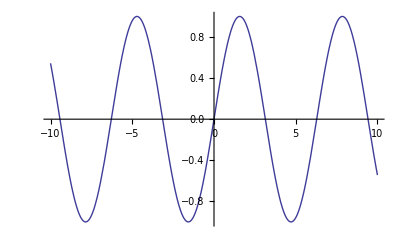

```mathematica
f[x_]:=Sin[x];
Plot[f[x],{x,-10,10}]
```

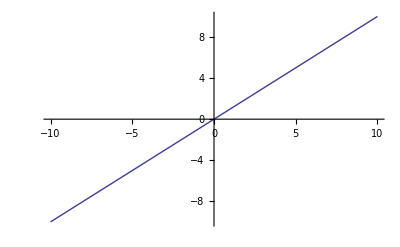

```mathematica
g[x_]:=x
Plot[g[x],{x,-10,10}]
```

Now the question is how we plot "f[x].g[x] or others " in the same graph?

So answering to this type of  questions our presentation topic “Section- 3.8” will help you.

-Graphics-

So let’s start

SuperImposing Plots :-

Two view two or more plots together, If you simply want to plot several functions on the same set of axes, enter a list containing these functions as the first argument to the Plot command and you will have it :

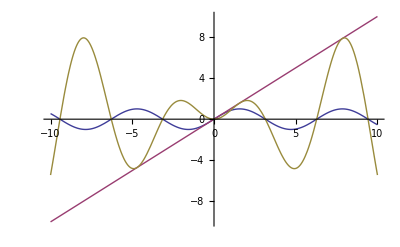

```mathematica
f[x_]:=Sin[x];
g[x_]:=x;
Plot[{f[x],g[x],f[x]*g[x]},{x,-10,10}]
```

Comment :-

We see the three functions are given three distinct colors. To better distinguish between them we have another command.

Using Tooltip :-

Tooltip command wrap the list of functions. After using this command when we mouseover any curve in the resulting plot, a tooltip will pop up displaying the function’s expression.

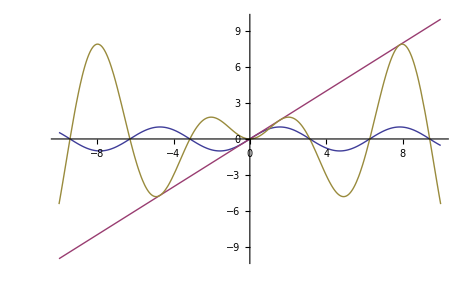

```mathematica
Plot[Tooltip[{f[x],g[x],f[x]*g[x]}],{x,-10,10}]
```

Comment :-

Output in printed form is indistinguishable from the prior output, so this feature is only useful in a live session. We another useful command.

Using PlotStyle :-

PlotStyle use to change the appearence of the three functions. This is sometimes useful for printed output when using black and white printed. Just set PlotStyle to a list of three directives. These will be applied to the function (In ordered listed).

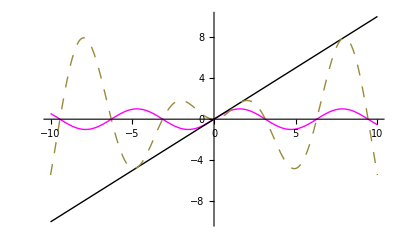

```mathematica
Plot[{f[x],g[x],f[x]*g[x]},{x,-10,10},
PlotStyle->{Magenta,Black,Dashing[{.02}]}]
```

Comment :-

This is some times useful for printed output when using black and white printed. With a little extra work we can add something more interesting.

Using PlotLegends :-

The option PlotLegends is set to the list of labels to be placed in the legend box. In this case we just used the function themselves, but textual expressions or strings (expressions enclosed in double quotes) are also fine.

```mathematica
TabView[{Plot[{f[x],g[x],f[x]*g[x]},{x,-10,10},
PlotStyle->{Red,Blue,Dashing[{.01}]},
PlotLegends->{f[x],g[x],f[x]*g[x]}],
Plot[{f[x],g[x],f[x]*g[x]},{x,-10,10},PlotStyle->{Red,Blue,Dashing[{.01}]},
PlotLegends->{"f[x]","g[x]","f[x]*g[x]"}]}]
```

12

Note :-

In older version of mathematica (Mathematica- 7.0)  Plotlegends command some times doesn’t work . So we need to give a command Needs[“PlotLegends”]  for working this command.

Comment :-

We can change the position using LegendPosition  command. Ex- the setting [-1,-1] placed the legend in the lower left .

Using Drawing Tool :-

Simply plot your functions , then click on the output image and use the drawing tools to place on it.

```mathematica
Plot[{2^x,x^2,1/x},{x,-1,1},PlotRange->{0,3},PlotStyle->{Gray,Directive[Dashed,Blue],
Directive[Dotted,Red]}]
```

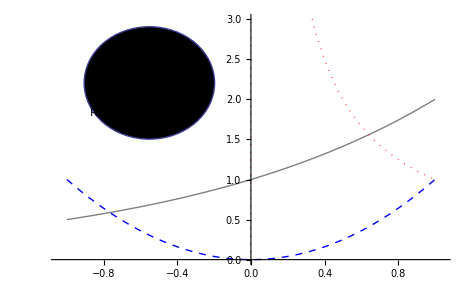

Comment :-

Here we have used the drawing tools to add a legend.

If  you need to superimpoe a large number of plots, you can use "Mathematica's Table" command to generate list of functions :

Table Command :-

Table[expr,n] generates a list of n copies of expr. Table[expr,{i,imax}] generates a list of the values of expr when i runs from  1  to...

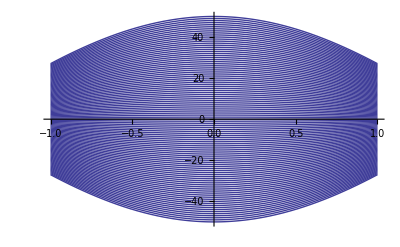

```mathematica
Plot[Table[{n*Cos[x]},{n,-50,50}],{x,-1,1},PlotRange->50]
```

Comment :-

The example above , the processing time is reduced and curves become individually colored if one replaces Table[f[t+x],{t,min,max}] by Evaluate[Table[f[t+x],{t,min,max}]] .

Using Evaluate :-

Evaluate[expr] causes expr to be evaluated even if it appears as the argument of a function whose attributes specify that it should be held.

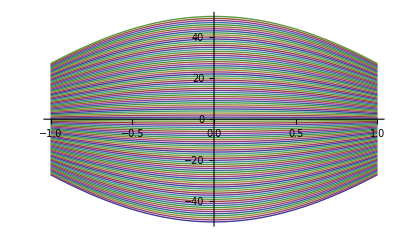

```mathematica
Plot[Evaluate[Table[{n*Cos[x]},{n,-50,50}],{x,-1,1},PlotRange->50]]
```

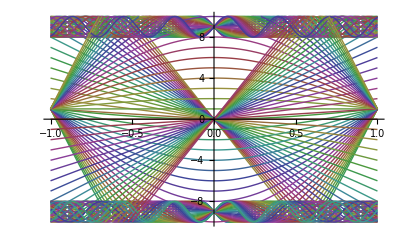

```mathematica
Plot[Evaluate[Table[{Sin[m*y]-9,Sin[m*y]+9,m*y,m*Cos[ y Pi/2]+1},
{m,-20,20}],{y,-1,1},PlotRange->10]]
```

Producing Filled Plots :-

Filling is an option for ListPlot, Plot, Plot3D, and related functions that specifies what filling to add under points, curves, and surfaces.

The following settings can be used:
None	                              no filling (default)
Axis	                              fill to the axis
Bottom                             	 fill to the bottom of the plot
Top	                              fill to the top of the plot
v	                              fill to value v
{m}	                              fill to the m^th object
{i1->p1,i2->p2,…}	 fill from object ik to pk
{i1->{p1,g1},…}	                use directive gk for the k^th filling
{i1->{p1,{g1-,g1+},…}}	 use g1- below and g1+ above

Example :-

One can shade the region between a plot and the axes as follows:

```mathematica
Plot[Sin[x], {x, -2 Pi,2 Pi}, Filling -> Axis]
```

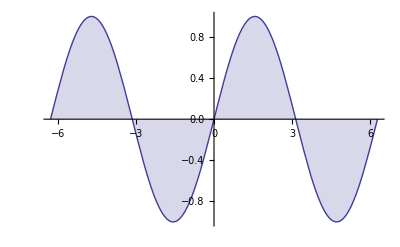

And one can shade the region between two curves like so :

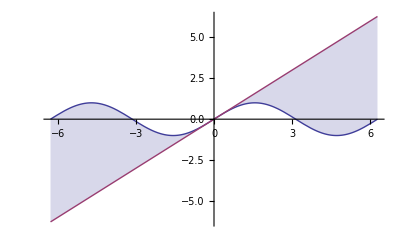

```mathematica
Plot[{Sin[x],x}, {x, -2 Pi,2 Pi}, Filling ->{1}]
```

Now Filling command becomes more intersting when we have more than two graphs. There are many ways to shade the various regions between them.

Below, filling is added from the first to the third, and from the second function to the top of the plot.

Example-1

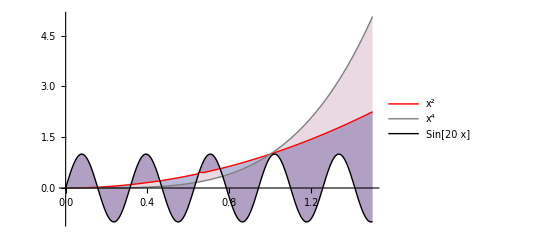

```mathematica
Plot[{x^2, x^4,Sin[20 x]}, {x, 0,1.5},PlotLegends->{x^2,x^4,Sin[20 x]},PlotStyle->{Red,Gray,Black},PlotRange->All,
Filling ->{1->{3},2->{3},3->{1}}]
```

Example-2

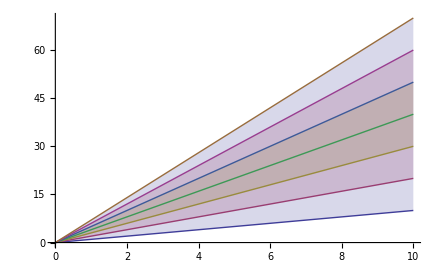

```mathematica
Plot[Evaluate[Table[ n x, {n, 7}]], {x,0, 10}, 
Filling -> {1->{7},2->{6},3->{5},4->{4}}]
```

Example-3

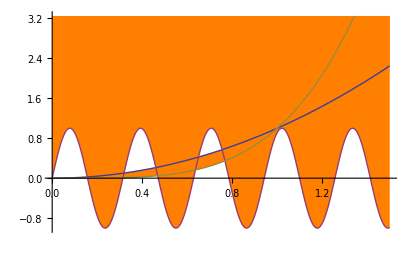

```mathematica
Plot[{x^2,Sin[20x],x^4},{x,0,1.5},Filling->{1->{3},2->Top},FillingStyle->Orange,
PlotRange->Automatic]
```

Example-4

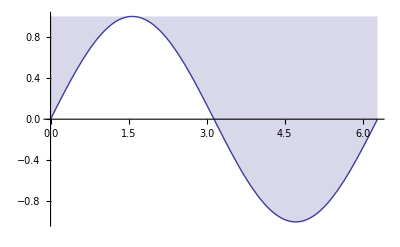
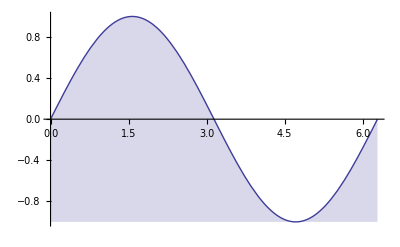
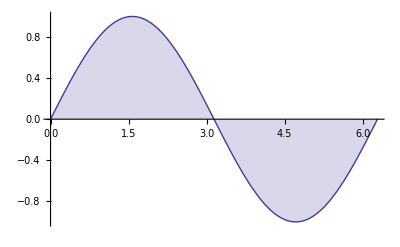
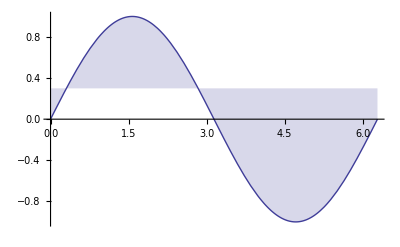

```mathematica
Table[Plot[Sin[x], {x, 0, 2 Pi},Filling -> f], {f, {Top, Bottom, Axis, 0.3}}]
```

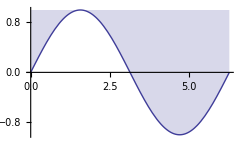
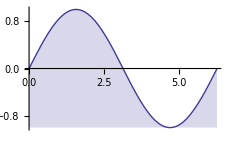
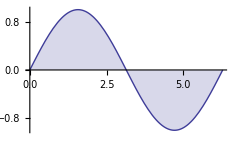
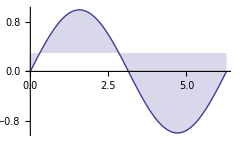

Example-5

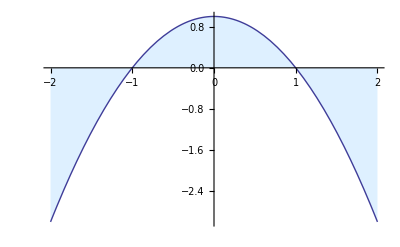

```mathematica
Plot[1-x^2,{x,-2,2},Filling->Axis,FillingStyle->LightBlue]
```

Superimposing Graphics :-

We can superimpose two or more graphs or picture using Show command.

Show :-

We can use this command  two basic types:

[1]  Show[graphics,options] =  shows graphics with the specified options added.

[2]  Show[g1,g2,…] = shows several graphics combined.

Now we demonstrate this by assigning names to the component images and suppressing their individual output with semicolons.

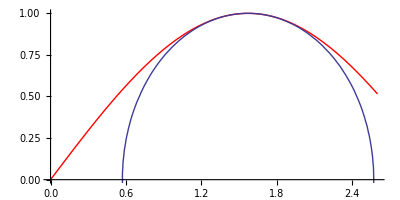

```mathematica
p1= Plot[Sin[x],{ x, 0, 2.6}, AspectRatio->0.5,PlotStyle->Red]; 
p2= ContourPlot[( x-π/2)^2 +y^2==1 ,{x, 0, 3},{ y, -1, 1 }];
Show[p1, p2]
```

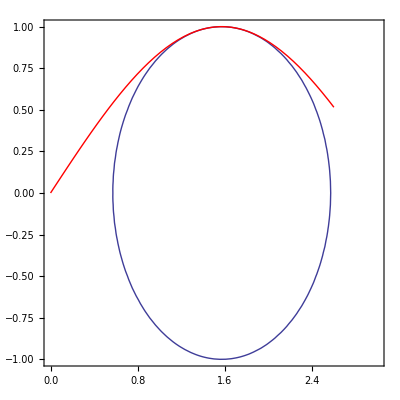

```mathematica
Show[p2,p1]
```

Note :- The order of the component images listed within Show is the order in which they are rendered.

one more example to show this is:-

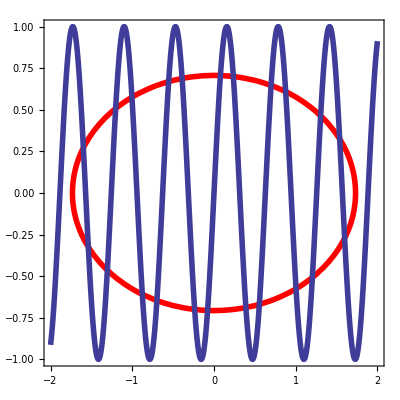

```mathematica
ellipse=ContourPlot[(x^2)/3+2*y^2==1,{ x,- 2, 2},{ y, -1,1},
ContourStyle->Directive[Red,Thickness[.01]]];
squiggle= Plot[Sin[10 x],{x, -2,2},PlotStyle->Directive[Dash,Thickness[.01]]];
Show[ellipse,squiggle]
```

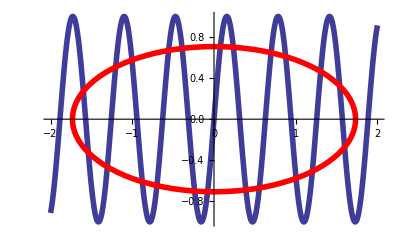

```mathematica
Show[squiggle,ellipse]
```

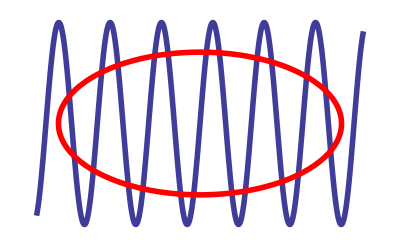

```mathematica
Show[squiggle,ellipse,Axes->False]
```

Comment :- One may also include within Show any option accepted by Graphics. Such option can be used to override setting inherited from the component images. Also keep in mind that while Show  is an extremly useful and versatile command, it is often not needed. To plot two function together, for instance, recall that one can simply provide a list of the two function as the first argument to Plot.

Graphics Side-by-side :-

It is used in arranging graphics Side-by-Side and to simply create a list of graphics.

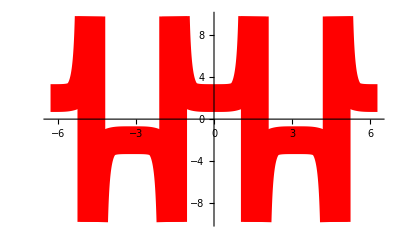
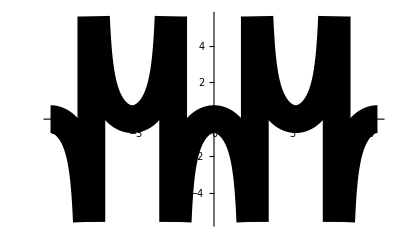

```mathematica
{a=Plot[Cos[x]+Sec[x],{x,-2π,2π},PlotStyle->Directive[Red,Thickness[.05]]],
b=Plot[Cos[x]-Sec[x],{x,-2π,2π},PlotStyle->Directive[Black,Thickness[.05]]]}
```

Comment :-  The curly brackets enclosing the list seperated by commas are displayed        in the output.

A better way to accomplish a side by side display is to use graphics row. It will integrate this list of individual Graphics objects into one graphic that can be resized or moved as a whole.

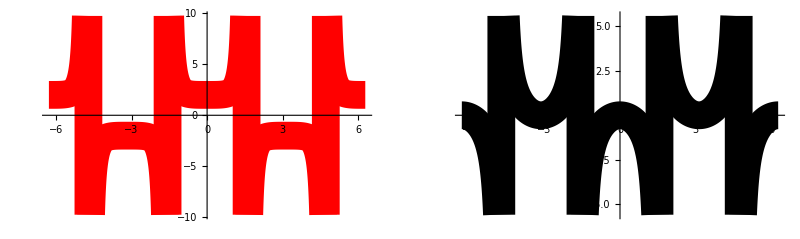

```mathematica
GraphicsRow[{a,b}]
```

The list of graphics can be generated programmatically, using the command Table. The Frame, FrameStyle, and Dividers options may be used to add frames around each item, or to place divider lines between some of them.

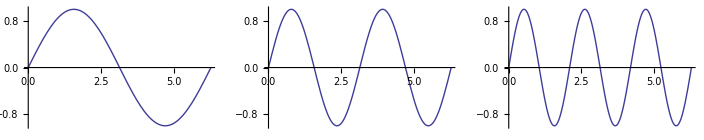

```mathematica
GraphicsRow[Table[Plot[Sin[m*x],{x,0,2π}],{m,3}],Frame->All,FrameStyle->Dotted]
```

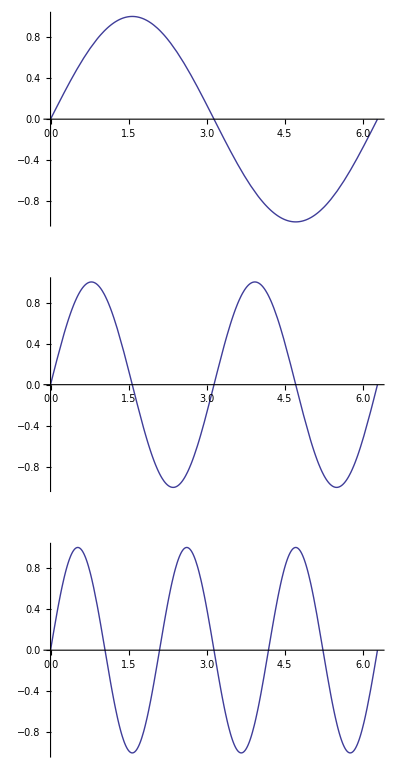

```mathematica
GraphicsColumn[Table[Plot[Sin[m*x],{x,0,2π}],{m,3}],Frame->All,FrameStyle->Dashed]
```

Graphics in a Grid :-

To lay out graphics in a grid pattern we have GraphicsGrid command . The syntax and many of the option are same as for Grid.

Question :-  Make the following grid showing the plots of trigonometric functions i.e. the functions of the form Csc[m x] and Sec[m x], for real parameters m and with domain 0<x<2π .

```mathematica
GraphicsGrid[{Table[Plot[Csc[m x],{x,0,2Pi},Axes->False],{m,5}],
Table[Plot[Sec[m x],{x,0,2Pi},Axes->False],{m,5}]},Frame->All,FrameStyle->Gray]
```

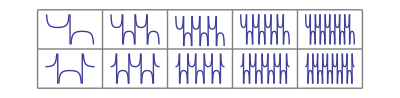

There is a GraphicGrid command to lay out graphics in a grid pattern.

For example if we want to grid the text we use the command TextGrid.

```mathematica
Text[Grid[{{"first","second"},{"third","fourth"}}]]
```

first | second
third | fourth

Comment :- The main difference between Grid and GraphicsRow or GraphicsGrid is that the output of these latter commands is a single  graphic that may be edited as such, for instance using the drawing tools. The entire output can be resized by selecting it and dragging a handle. In a plain Grid, only the individual component graphics can be edited.

Some Applications :-

```mathematica
GraphicsRow[{{Plot[1/x^4,{x,0,1},PlotStyle->Directive[Red,Thickness[.1]]]},
{ContourPlot[x^2+y^2==4,{x,-2,2},{y,-2,2},ContourStyle->Directive[Red,Thickness[.1]]]},
{Plot[Abs[-2 x],{x,-2,2},PlotStyle->Directive[Red,Thickness[.1]]]},
{ContourPlot[x==-3 Abs[Sin[y]],{x,0,-3},{y,-Pi,Pi},ContourStyle->Directive[Red,Thickness[.1]]]}}]
```

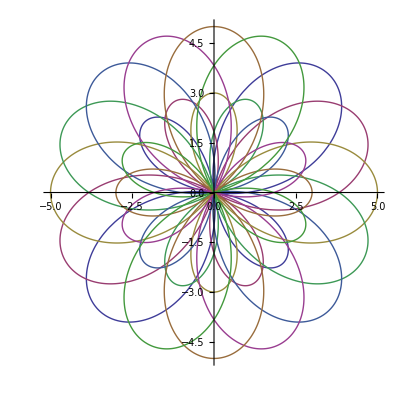

```mathematica
PolarPlot[Evaluate[Table[1+4Sin[2(t+i Pi/8)],{i,0,7}]],{t,0,2 Pi}]
```

```mathematica
Manipulate[Plot[Sin[n1 x^2]+Sin[n2 x/3],{x,0,2 Pi},
Filling->filling,PlotRange->2,PlotStyle-> color],
{n1,1,20},{n2,1,30},{filling,{None,2,1.5,1,0.5,0,-0.5,-1,-1.5,-2}}
,{filling,-2,2},{color,Blue}]
```

Refrences :-

[1]   http://www.wolfram.com/broadcast/video.php?c=299&v=652

[2]  https://reference.wolfram.com/language/?source=nav

[3]  https://mathematica.stackexchange.com/

[4]  https://www.wolframcloud.com/

[5]  Cambridge University Press the Edinburgh Bulding, Cambridge CB28RU, Uk

www.cambridge.org

Information on this title:www.cambridge.org/9780521177892

B. Torrence  and E. Torrence 2009

-Graphics-